# Parse data files to visualize/analyze geometry results

```mathematica
SetDirectory["/Users/swsides/psall/polyswift/psutils/python"]
FileNames[]
```

/Users/swsides/psall/polyswift/psutils/python

{CMakeLists.txt,geometry.dat,geometry.png,geometry.py,geometry.pyc,geometryVars.py,geometryVars.pyc,geovis.m,geovis.nb,interfacePG.pre,interfacePG-series.py,polyswift.py,polyswift-vis.py,psDumpHistory.py,ps-move.py,psPlotHistory.py,psPlotHistoryRPA.py,pspp-gen.py,ps-run.py.in,ps-run-series.py,psVis.py.in,.svn}

```mathematica
(* Input Data *)
tmp=readFile["geometry.dat",1];
```

```mathematica
(* Parse for 2D or 3D *)
If[Last[tmp][[3]]==0,

flag2D=True;
geoDat=getColumns[tmp,{1,2,4}],

dims=Last[tmp];
xdims=dims[[1]];
ydims=dims[[2]];
zdims=dims[[3]];
flag2D=False;
geoDat=tmp
];
```

```mathematica
If[flag2D==False,
fig=ListContourPlot3D[geoDat,Contours->{0.5},
MaxPlotPoints->60,ImageSize->600,
AxesLabel->{"x","y","z"},
PlotRange->{{0,xdims+1},{0,ydims+1},{0,zdims+1}}]
]
```

```mathematica
If[flag2D==True,
fig=ListPlot3D[geoDat,
PlotRange->All,
AxesLabel->{"x","y"},
ImageSize->800]
]

Print["Creating image and exporting to geometry.png"]
Export["geometry.png",fig]
```

```mathematica
?ListContourPlot
```

ListContourPlot[array] generates a contour plot from an array of height values. 
ListContourPlot[{{x_1,y_1,f_1},{x_2,y_2,f_2},…}] generates a contour plot from values defined at specified points.

```mathematica
Options[ListContourPlot]
```

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ContourLabels→Automatic,ContourLines→True,Contours→Automatic,ContourShading→Automatic,ContourStyle→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,LabelStyle→{},LightingAngle→None,MaxPlotPoints→Automatic,Mesh→None,MeshFunctions→{},MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→{Full,Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

```mathematica
?ColorFunction
```

ColorFunction is an option for graphics functions which specifies a function to apply to determine colors of elements.

```mathematica
geoDat
```

{{0,0,0.},{0,1,0.},{0,2,0.},{0,3,0.},{0,4,0.},{0,5,0.},{0,6,0.},{0,7,0.},{0,8,0.},{0,9,0.},{0,10,0.},{0,11,0.},{0,12,0.},{0,13,0.},{0,14,0.},{0,15,0.},{0,16,0.},{0,17,0.},{0,18,0.},{0,19,0.},{0,20,0.},{0,21,0.},{0,22,0.},«14034»,{127,87,0.},{127,88,0.},{127,89,0.},{127,90,0.},{127,91,0.},{127,92,0.},{127,93,0.},{127,94,0.},{127,95,0.},{127,96,0.},{127,97,0.},{127,98,0.},{127,99,0.},{127,100,0.},{127,101,0.},{127,102,0.},{127,103,0.},{127,104,0.},{127,105,0.},{127,106,0.},{127,107,0.},{127,108,0.},{127,109,0.}}

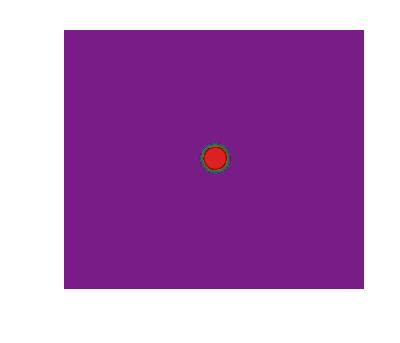

Creating image and exporting to geometry.png

photonic-surface.png

```mathematica
fig=ListContourPlot[geoDat,
PlotRange->All,
AxesLabel->{"x","y"},
ImageSize->400,AspectRatio->110.0/128.0,
Frame->None,
Contours->4,ColorFunction->"Rainbow"]

Print["Creating image and exporting to geometry.png"]
Export["photonic-surface.png",fig]
```